```mathematica
$Assumptions={τ>0,γ>0,ω0>0,√(ω0^2-γ^2/4)>0,τ>t>0,τ>u>0};
```

```mathematica
Psi[t_]=Exp[-γ/2 Abs[t]](Cos[√(ω0^2-γ^2/4)t]+γ/(2 √(ω0^2-γ^2/4))Sin[√(ω0^2-γ^2/4)Abs[t]]);
dPsi[t_]=-(2 ⅇ^(-1/2 γ Abs[t]) ω0^2 Sin[t √(-γ^2/4+ω0^2)])/(√(-γ^2+4 ω0^2));
ddPsi[t_]=-ⅇ^(-1/2 γ Abs[t]) ω0^2 Cos[t √(-γ^2/4+ω0^2)]+(ⅇ^(-1/2 γ Abs[t]) γ ω0^2 Sin[Abs[t] √(-γ^2/4+ω0^2)])/(√(-γ^2+4 ω0^2));
```

```mathematica
Clear[γ,ω0,Wh3]

τR=γ/ω0^2;
g[t_]=(t+τR)/(τ+2τR)+2(γ/ω0^2)/(τ+2γ/ω0^2)(HeavisideTheta[t]-HeavisideTheta[τ-t]);

p[t_]=1/τ;
popt[t_]=1/(τ+2γ/ω0^2)+2(γ/ω0^2)/(τ+2γ/ω0^2)(DiracDelta[t]+DiracDelta[τ-t]);

hCE[t_]=-(t/τ-1/2)+8(t/τ-1/2)^3+1/2;
```

```mathematica
W0[τ_]=Expand[Simplify[Psi[0]/2+Integrate[dPsi[τ-t]g[t],{t,0,τ}]-1/2 Integrate[ddPsi[t-u]g[t]g[u],{t,0,τ},{u,0,τ}]]]
```

(2 γ^2)/((2 γ+τ ω0^2)^2)+ω0^2/((2 γ+τ ω0^2)^2)+(γ τ ω0^2)/((2 γ+τ ω0^2)^2)-(ⅇ^(-(γ τ)/2) ω0^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/((2 γ+τ ω0^2)^2)+(ⅇ^(-(γ τ)/2) γ ω0^2 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(√(-γ^2+4 ω0^2) (2 γ+τ ω0^2)^2)

```mathematica
WCE[τ_]=Expand[Simplify[Psi[0]/2+Integrate[dPsi[τ-t]hCE[t],{t,0,τ}]-1/2 Integrate[ddPsi[t-u]hCE[t]hCE[u],{t,0,τ},{u,0,τ}]]]
```

-(2304 γ^6)/(τ^6 ω0^12)+(11520 γ^4)/(τ^6 ω0^10)-(13824 γ^2)/(τ^6 ω0^8)+(96 γ^4)/(τ^4 ω0^8)+2304/(τ^6 ω0^6)-(288 γ^2)/(τ^4 ω0^6)+(48 γ^3)/(τ^3 ω0^6)+96/(τ^4 ω0^4)-(96 γ)/(τ^3 ω0^4)-(25 γ^2)/(τ^2 ω0^4)+25/(τ^2 ω0^2)+(21 γ)/(5 τ ω0^2)+(2304 ⅇ^(-(γ τ)/2) γ^6 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^12)-(11520 ⅇ^(-(γ τ)/2) γ^4 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^10)+(2304 ⅇ^(-(γ τ)/2) γ^5 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^10)+(13824 ⅇ^(-(γ τ)/2) γ^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^8)-(9216 ⅇ^(-(γ τ)/2) γ^3 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^8)+(1056 ⅇ^(-(γ τ)/2) γ^4 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^8)-(2304 ⅇ^(-(γ τ)/2) Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^6)+(6912 ⅇ^(-(γ τ)/2) γ Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^6)-(3168 ⅇ^(-(γ τ)/2) γ^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^6)+(240 ⅇ^(-(γ τ)/2) γ^3 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^3 ω0^6)+(1056 ⅇ^(-(γ τ)/2) Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^4)-(480 ⅇ^(-(γ τ)/2) γ Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^3 ω0^4)+(25 ⅇ^(-(γ τ)/2) γ^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^4)-(25 ⅇ^(-(γ τ)/2) Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^2)+(2304 ⅇ^(-(γ τ)/2) γ^7 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^12 √(-γ^2+4 ω0^2))-(16128 ⅇ^(-(γ τ)/2) γ^5 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^10 √(-γ^2+4 ω0^2))+(2304 ⅇ^(-(γ τ)/2) γ^6 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^10 √(-γ^2+4 ω0^2))+(32256 ⅇ^(-(γ τ)/2) γ^3 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^8 √(-γ^2+4 ω0^2))-(13824 ⅇ^(-(γ τ)/2) γ^4 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^8 √(-γ^2+4 ω0^2))+(1056 ⅇ^(-(γ τ)/2) γ^5 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^8 √(-γ^2+4 ω0^2))-(16128 ⅇ^(-(γ τ)/2) γ Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^6 √(-γ^2+4 ω0^2))+(20736 ⅇ^(-(γ τ)/2) γ^2 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^6 √(-γ^2+4 ω0^2))-(5280 ⅇ^(-(γ τ)/2) γ^3 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^6 √(-γ^2+4 ω0^2))+(240 ⅇ^(-(γ τ)/2) γ^4 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^3 ω0^6 √(-γ^2+4 ω0^2))-(4608 ⅇ^(-(γ τ)/2) Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^4 √(-γ^2+4 ω0^2))+(5280 ⅇ^(-(γ τ)/2) γ Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^4 √(-γ^2+4 ω0^2))-(960 ⅇ^(-(γ τ)/2) γ^2 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^3 ω0^4 √(-γ^2+4 ω0^2))+(25 ⅇ^(-(γ τ)/2) γ^3 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^4 √(-γ^2+4 ω0^2))+(480 ⅇ^(-(γ τ)/2) Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^3 ω0^2 √(-γ^2+4 ω0^2))-(75 ⅇ^(-(γ τ)/2) γ Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^2 √(-γ^2+4 ω0^2))

```mathematica
W0[τ_]=(2 γ^2)/((2 γ+τ ω0^2)^2)+ω0^2/((2 γ+τ ω0^2)^2)+(γ τ ω0^2)/((2 γ+τ ω0^2)^2)-(ⅇ^(-(γ τ)/2) ω0^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/((2 γ+τ ω0^2)^2)+(ⅇ^(-(γ τ)/2) γ ω0^2 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(√(-γ^2+4 ω0^2) (2 γ+τ ω0^2)^2);
WCE[τ_]=-(2304 γ^6)/(τ^6 ω0^12)+(11520 γ^4)/(τ^6 ω0^10)-(13824 γ^2)/(τ^6 ω0^8)+(96 γ^4)/(τ^4 ω0^8)+2304/(τ^6 ω0^6)-(288 γ^2)/(τ^4 ω0^6)+(48 γ^3)/(τ^3 ω0^6)+96/(τ^4 ω0^4)-(96 γ)/(τ^3 ω0^4)-(25 γ^2)/(τ^2 ω0^4)+25/(τ^2 ω0^2)+(21 γ)/(5 τ ω0^2)+(2304 ⅇ^(-(γ τ)/2) γ^6 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^12)-(11520 ⅇ^(-(γ τ)/2) γ^4 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^10)+(2304 ⅇ^(-(γ τ)/2) γ^5 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^10)+(13824 ⅇ^(-(γ τ)/2) γ^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^8)-(9216 ⅇ^(-(γ τ)/2) γ^3 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^8)+(1056 ⅇ^(-(γ τ)/2) γ^4 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^8)-(2304 ⅇ^(-(γ τ)/2) Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^6)+(6912 ⅇ^(-(γ τ)/2) γ Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^6)-(3168 ⅇ^(-(γ τ)/2) γ^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^6)+(240 ⅇ^(-(γ τ)/2) γ^3 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^3 ω0^6)+(1056 ⅇ^(-(γ τ)/2) Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^4)-(480 ⅇ^(-(γ τ)/2) γ Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^3 ω0^4)+(25 ⅇ^(-(γ τ)/2) γ^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^4)-(25 ⅇ^(-(γ τ)/2) Cos[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^2)+(2304 ⅇ^(-(γ τ)/2) γ^7 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^12 √(-γ^2+4 ω0^2))-(16128 ⅇ^(-(γ τ)/2) γ^5 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^10 √(-γ^2+4 ω0^2))+(2304 ⅇ^(-(γ τ)/2) γ^6 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^10 √(-γ^2+4 ω0^2))+(32256 ⅇ^(-(γ τ)/2) γ^3 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^8 √(-γ^2+4 ω0^2))-(13824 ⅇ^(-(γ τ)/2) γ^4 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^8 √(-γ^2+4 ω0^2))+(1056 ⅇ^(-(γ τ)/2) γ^5 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^8 √(-γ^2+4 ω0^2))-(16128 ⅇ^(-(γ τ)/2) γ Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^6 ω0^6 √(-γ^2+4 ω0^2))+(20736 ⅇ^(-(γ τ)/2) γ^2 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^6 √(-γ^2+4 ω0^2))-(5280 ⅇ^(-(γ τ)/2) γ^3 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^6 √(-γ^2+4 ω0^2))+(240 ⅇ^(-(γ τ)/2) γ^4 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^3 ω0^6 √(-γ^2+4 ω0^2))-(4608 ⅇ^(-(γ τ)/2) Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^5 ω0^4 √(-γ^2+4 ω0^2))+(5280 ⅇ^(-(γ τ)/2) γ Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^4 ω0^4 √(-γ^2+4 ω0^2))-(960 ⅇ^(-(γ τ)/2) γ^2 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^3 ω0^4 √(-γ^2+4 ω0^2))+(25 ⅇ^(-(γ τ)/2) γ^3 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^4 √(-γ^2+4 ω0^2))+(480 ⅇ^(-(γ τ)/2) Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^3 ω0^2 √(-γ^2+4 ω0^2))-(75 ⅇ^(-(γ τ)/2) γ Sin[1/2 τ √(-γ^2+4 ω0^2)])/(τ^2 ω0^2 √(-γ^2+4 ω0^2));
```

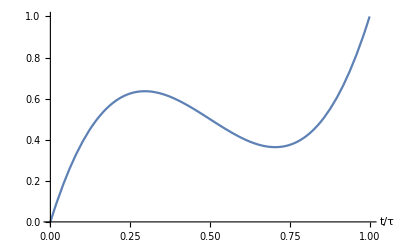

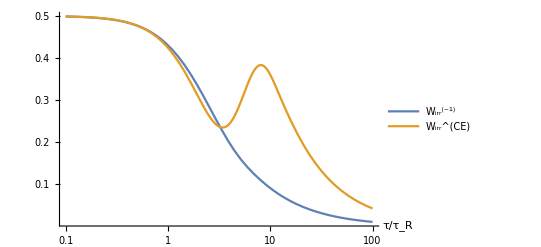

```mathematica
γ=1;
ω0=1;
τR=γ/ω0^2;
a=-1;

Plot[a(t-1/2)+4(1-a)(t-1/2)^3+1/2,{t,0,1},PlotRange->{{0,1},{0,1}},AxesLabel->{"t/τ"}]

LogLinearPlot[{Legended[W0[τ],"W_irr^(-1)"],Legended[WCE[τ],"W_irr^(CE)"]},{τ,0.1,100},PlotRange->Full,AxesLabel->{"τ/τ_R"},PlotLegends->Placed[{},{Right,Center}]]
Clear[τR,γ,ω0,a,b]
```

New try

```mathematica
$Assumptions={τ>0,γ>0,ω0>0,√(ω0^2-γ^2/4)>0,τ>=t>=0,τ>=u>=0};
```

```mathematica
Psi[t_]=Exp[-γ/2 Abs[t]](Cos[√(ω0^2-γ^2/4)t]+γ/(2 √(ω0^2-γ^2/4))Sin[√(ω0^2-γ^2/4)Abs[t]]);
```

```mathematica
Clear[γ,ω0,Wh3]

τR=γ/ω0^2;
g[t_]=(t+τR)/(τ+2τR);

popt[t_]=1/(τ+2γ/ω0^2)+2(γ/ω0^2)/(τ+2γ/ω0^2)(DiracDelta[t]+DiracDelta[τ-t]);

pCE[t_]=-1/τ+(24 (-1/2+t/τ)^2)/τ;
```

```mathematica
Integrate[Psi[t-u]pCE[t]pCE[u],{t,0,τ},{u,0,t}];
```

```mathematica
Aux1[τ_]=Integrate[Psi[t-u],{t,0,τ},{u,0,t}]/((τ+2γ/ω0^2)^2)
```

1/((τ+(2 γ)/ω0^2)^2 ω0^4 √(-γ^2+4 ω0^2))ⅇ^(-(γ τ)/2) (-ⅇ^((γ τ)/2) γ^2 √(-γ^2+4 ω0^2)+ⅇ^((γ τ)/2) ω0^2 √(-γ^2+4 ω0^2)+ⅇ^((γ τ)/2) γ τ ω0^2 √(-γ^2+4 ω0^2)+γ^2 √(-γ^2+4 ω0^2) Cos[1/2 τ √(-γ^2+4 ω0^2)]-ω0^2 √(-γ^2+4 ω0^2) Cos[1/2 τ √(-γ^2+4 ω0^2)]+γ^3 Sin[1/2 τ √(-γ^2+4 ω0^2)]-3 γ ω0^2 Sin[1/2 τ √(-γ^2+4 ω0^2)])

```mathematica
Aux2[τ_]=(γ/ω0^2)/(τ+2γ/ω0^2)^2 Integrate[Psi[t]+Psi[τ-t],{t,0,τ}]
```

(2 ⅇ^(-(γ τ)/2) γ (ⅇ^((γ τ)/2) γ √(-γ^2+4 ω0^2)-γ √(-γ^2+4 ω0^2) Cos[1/2 τ √(-γ^2+4 ω0^2)]-γ^2 Sin[1/2 τ √(-γ^2+4 ω0^2)]+2 ω0^2 Sin[1/2 τ √(-γ^2+4 ω0^2)]))/((τ+(2 γ)/ω0^2)^2 ω0^4 √(-γ^2+4 ω0^2))

```mathematica
Aux3[τ_]=(γ^2 (Psi[0]+Psi[τ]))/((τ+(2 γ)/ω0^2)^2 ω0^4);
```

```mathematica
Expand[Assuming[τ>0,Simplify[Aux1[τ]+Aux2[τ]+Aux3[τ]]]]
```

(2 γ^2)/((2 γ+τ ω0^2)^2)+ω0^2/((2 γ+τ ω0^2)^2)+(γ τ ω0^2)/((2 γ+τ ω0^2)^2)-(ⅇ^(-(γ τ)/2) ω0^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/((2 γ+τ ω0^2)^2)+(ⅇ^(-(γ τ)/2) γ ω0^2 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(√(-γ^2+4 ω0^2) (2 γ+τ ω0^2)^2)

```mathematica
WCE[τ_]=1/(5 τ^6 ω0^12 √(-γ^2+4 ω0^2))ⅇ^(-(γ τ)/2) (-11520 ⅇ^((γ τ)/2) γ^6 √(-γ^2+4 ω0^2)+57600 ⅇ^((γ τ)/2) γ^4 ω0^2 √(-γ^2+4 ω0^2)-69120 ⅇ^((γ τ)/2) γ^2 ω0^4 √(-γ^2+4 ω0^2)+480 ⅇ^((γ τ)/2) γ^4 τ^2 ω0^4 √(-γ^2+4 ω0^2)+11520 ⅇ^((γ τ)/2) ω0^6 √(-γ^2+4 ω0^2)-1440 ⅇ^((γ τ)/2) γ^2 τ^2 ω0^6 √(-γ^2+4 ω0^2)+240 ⅇ^((γ τ)/2) γ^3 τ^3 ω0^6 √(-γ^2+4 ω0^2)+480 ⅇ^((γ τ)/2) τ^2 ω0^8 √(-γ^2+4 ω0^2)-480 ⅇ^((γ τ)/2) γ τ^3 ω0^8 √(-γ^2+4 ω0^2)-125 ⅇ^((γ τ)/2) γ^2 τ^4 ω0^8 √(-γ^2+4 ω0^2)+125 ⅇ^((γ τ)/2) τ^4 ω0^10 √(-γ^2+4 ω0^2)+21 ⅇ^((γ τ)/2) γ τ^5 ω0^10 √(-γ^2+4 ω0^2)+11520 γ^6 √(-γ^2+4 ω0^2) Cos[1/2 τ √(-γ^2+4 ω0^2)]-57600 γ^4 ω0^2 √(-γ^2+4 ω0^2) Cos[1/2 τ √(-γ^2+4 ω0^2)]+11520 γ^5 τ ω0^2 √(-γ^2+4 ω0^2) Cos[1/2 τ √(-γ^2+4 ω0^2)]+69120 γ^2 ω0^4 √(-γ^2+4 ω0^2) Cos[1/2 τ √(-γ^2+4 ω0^2)]-46080 γ^3 τ ω0^4 √(-γ^2+4 ω0^2) Cos[1/2 τ √(-γ^2+4 ω0^2)]+5280 γ^4 τ^2 ω0^4 √(-γ^2+4 ω0^2) Cos[1/2 τ √(-γ^2+4 ω0^2)]-11520 ω0^6 √(-γ^2+4 ω0^2) Cos[1/2 τ √(-γ^2+4 ω0^2)]+34560 γ τ ω0^6 √(-γ^2+4 ω0^2) Cos[1/2 τ √(-γ^2+4 ω0^2)]-15840 γ^2 τ^2 ω0^6 √(-γ^2+4 ω0^2) Cos[1/2 τ √(-γ^2+4 ω0^2)]+1200 γ^3 τ^3 ω0^6 √(-γ^2+4 ω0^2) Cos[1/2 τ √(-γ^2+4 ω0^2)]+5280 τ^2 ω0^8 √(-γ^2+4 ω0^2) Cos[1/2 τ √(-γ^2+4 ω0^2)]-2400 γ τ^3 ω0^8 √(-γ^2+4 ω0^2) Cos[1/2 τ √(-γ^2+4 ω0^2)]+125 γ^2 τ^4 ω0^8 √(-γ^2+4 ω0^2) Cos[1/2 τ √(-γ^2+4 ω0^2)]-125 τ^4 ω0^10 √(-γ^2+4 ω0^2) Cos[1/2 τ √(-γ^2+4 ω0^2)]+11520 γ^7 Sin[1/2 τ √(-γ^2+4 ω0^2)]-80640 γ^5 ω0^2 Sin[1/2 τ √(-γ^2+4 ω0^2)]+11520 γ^6 τ ω0^2 Sin[1/2 τ √(-γ^2+4 ω0^2)]+161280 γ^3 ω0^4 Sin[1/2 τ √(-γ^2+4 ω0^2)]-69120 γ^4 τ ω0^4 Sin[1/2 τ √(-γ^2+4 ω0^2)]+5280 γ^5 τ^2 ω0^4 Sin[1/2 τ √(-γ^2+4 ω0^2)]-80640 γ ω0^6 Sin[1/2 τ √(-γ^2+4 ω0^2)]+103680 γ^2 τ ω0^6 Sin[1/2 τ √(-γ^2+4 ω0^2)]-26400 γ^3 τ^2 ω0^6 Sin[1/2 τ √(-γ^2+4 ω0^2)]+1200 γ^4 τ^3 ω0^6 Sin[1/2 τ √(-γ^2+4 ω0^2)]-23040 τ ω0^8 Sin[1/2 τ √(-γ^2+4 ω0^2)]+26400 γ τ^2 ω0^8 Sin[1/2 τ √(-γ^2+4 ω0^2)]-4800 γ^2 τ^3 ω0^8 Sin[1/2 τ √(-γ^2+4 ω0^2)]+125 γ^3 τ^4 ω0^8 Sin[1/2 τ √(-γ^2+4 ω0^2)]+2400 τ^3 ω0^10 Sin[1/2 τ √(-γ^2+4 ω0^2)]-375 γ τ^4 ω0^10 Sin[1/2 τ √(-γ^2+4 ω0^2)]);
```

```mathematica
WNopt[τ_]=(2 γ^2)/((2 γ+τ ω0^2)^2)+ω0^2/((2 γ+τ ω0^2)^2)+(γ τ ω0^2)/((2 γ+τ ω0^2)^2)-(ⅇ^(-(γ τ)/2) ω0^2 Cos[1/2 τ √(-γ^2+4 ω0^2)])/((2 γ+τ ω0^2)^2)+(ⅇ^(-(γ τ)/2) γ ω0^2 Sin[1/2 τ √(-γ^2+4 ω0^2)])/(√(-γ^2+4 ω0^2) (2 γ+τ ω0^2)^2);
```

```mathematica
Limit[WNopt[τ],τ->0,Direction->"FromAbove"]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1/2

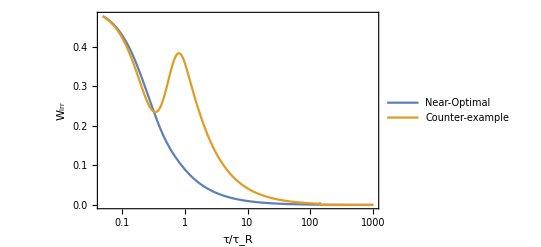

```mathematica
γ=10;
ω0=10;

LogLinearPlot[{WNopt[τ],WCE[τ]},{τ,0.05,1000},PlotRange->Full,Frame->True, FrameLabel->{"τ/τ_R","W_irr"},FrameStyle->Directive[Bold,Black,12],PlotLegends->Placed[{"Near-Optimal","Counter-example"},{Scaled[0.8],Scaled[0.8]}]]

Clear[γ,ω0,τP]
```

```mathematica
InverseLaplaceTransform[s^2,s,t]
```

DiracDelta''[t]